# The moulding of intra-specific trait variation by selection under ecological inheritance

### Iris Prigent and Charles Mullon Department of Ecology and Evolution University of Lausanne charles.mullon@unil.ch 06/03/2023

This notebook (written in Mathematica 12 and 13) derives the results presented in section 4 of our article entitled “The moulding of intra-specific trait variation by selection under ecological inheritance”, concerning the joint evolution of dispersal with the attack rate on a local renewable resource. See also Appendix F to our article for details.

## Joint evolution of dispersal with the attack rate on a local renewable resource

```mathematica
Clear["Global`*"];
```

## 1. Necessary components

We first define some components that are necessary to the analysis. Essentially, we formalize the model described in 4.1 of the main text, the quantities from Table 1 and Appendix F1.

### A. Traits

We define zi1, zj1 and zh1 as the attack rates of individuals indexed i, j and h, and z1 as the resident attack rate (resp. z_i1, z_j1, z_h1 and z_1 in the main text). Conversely, zi2, zj2 and zh2 are the dispersal probabilities of individuals i, j and h, and z1 is the resident attack rate (resp. z_i2, z_j2, z_h2 and z_2 in the main text).  For each trait, we define the vector zpall = {zip, zjp, zhp}, containing the value of that trait in the focal individual i, in one of its neighbour j, and another (distinct) neighbour h. This will allow us to define functions that can be applied to any trait z_p.

```mathematica
z2all={zi2,zj2,zh2};
z1all={zi1,zj1,zh1};
```

We also denote n the number of individuals per patch (we cannot use N  as in the main text,because it is a default function in Mathematica). The mean attack rate in a patch OverBar[z1] =(z̄)_1 is the sum of all traits within that patch divided by the number of individuals:

```mathematica
OverBar[z1] =1/n (zi1+zj1+zh1+(n-3)z1);
```

In a population monomorphic for the resident morph z = (z_1,  z_2), all traits are equal to the resident’s :

```mathematica
monopop = {zi1->z1  ,zj1->z1 ,zh1->z1 ,zi2->z2,zj2->z2,zh2->z2};
OverBar[z1] ==z1 /.monopop//FullSimplify
```

True

### B. Environmental dynamics

Here we define the  map ϵ_(t+1)=F(z_1,…,z_N,ϵ) (eq.1) for the ecological dynamics in this application of our model. The environmental state ϵ of a patch at generation t is the abundance of the resource in that patch before consumption. To obtain the resource dynamics between generation, we track the resource abundance from the beginning of an iteration of the life-cycle to the beginning of the next iteration.

#### • Intra - generational dynamics

We denote τ the intra-generational time,(running from 0 to T) and ϵ_(t,τ) the resource abundance at time τ  in generation t. Within generation, we assume that the resource dynamics are made of two phases: (i) a consumption phase from τ=0 to τ_1 and (ii) a renewal phase from τ= τ_1 to T.

i - Consumption phase

While 0⩽τ⩽τ_1 , the resource is being consumed by the consumers. An individual i in the patch consumes the resource at a rate given by its trait z_i1. Specifically,the rate of change in the amount ρi[τ] of resource collected by individual i at time τ  is ρ_i'[τ] = z_(1,i) ϵ[τ] (eq. 23) such that the total rate of resource intake is ∑_(i=1)^N ρ_i'[τ] = N (z̄)_1 ϵ[τ] . The rate of change in resource abundance is  then ϵ'[τ]= - ϵ[τ]N (z̄)_1 (eq. 24). Solving the system with initial conditions ρi[0]=0 and ϵ[0]=ϵ_(t,0), we obtain

```mathematica
Flatten[DSolve[  {ρi'[τ] == zi1 ϵ[τ],ϵ'[τ] == - n OverBar[z1] ϵ[τ],  ϵ[0] == ϵ0, ρi[0] == 0  },{ϵ,ρi},τ]]/.ϵ0->Subscript[ϵ, t,0]
```

{ϵ→Function[{τ},ⅇ^((-((-3+n) z1)-zh1-zi1-zj1) τ) ϵ_(t,0)],ρi→Function[{τ},-((-1+ⅇ^((-((-3+n) z1)-zh1-zi1-zj1) τ)) zi1 ϵ_(t,0))/(-3 z1+n z1+zh1+zi1+zj1)]}

At the end of the consumption phase (at time τ_i), the resource abundance is

```mathematica
Subscript[ϵ, t,Subscript[τ, 1]]:=ϵ[τ]/.
Flatten[DSolve[  {ρi'[τ] ==zi1 ϵ[τ],ϵ'[τ] == - n OverBar[z1] ϵ[τ],  ϵ[0] == ϵ0, ρi[0] == 0  },{ϵ,ρi},τ]]/.ϵ0->Subscript[ϵ, t,0]/.τ->τ1;
Subscript[ϵ, t,Subscript[τ, 1]]==Subscript[ϵ, t,0] ⅇ^(-τ1 n  OverBar[z1])//Simplify
```

True

```mathematica
(*eq. 25*)
```

and an individual i has consumed a resource amount

```mathematica
Subscript[ρ, i,Subscript[τ, 1]]:=ρi[τ]/.
Flatten[DSolve[  {ρi'[τ] == zi1 ϵ[τ],ϵ'[τ] == - n OverBar[z1] ϵ[τ],  ϵ[0] == ϵ0, ρi[0] == 0  },{ϵ,ρi},τ]]/.ϵ0->Subscript[ϵ, t,0]/.τ->τ1;
Subscript[ρ, i,Subscript[τ, 1]]==Subscript[ϵ, t,0](1-ⅇ^(- τ1 n OverBar[z1]))zi1/(n OverBar[z1])//Simplify
(*eq. 26*)
```

True

ii - Renewal phase

While τ_1 ⩽ τ ⩽ T, the resource grows logistically, according to  R'[τ]=γ_0  R[τ](1-R[τ]/k) (eq. 27)

```mathematica
DSolve[ { R'[τ]== Subscript[γ, 0]  R[τ](1-R[τ]/k), R[0] == Subscript[ϵ, t,Subscript[τ, 1]]},R,τ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{R→Function[{τ},(ⅇ^(3 z1 τ1+τ γ_0) k ϵ_(t,0))/(ⅇ^(n z1 τ1+zh1 τ1+zi1 τ1+zj1 τ1) k-ⅇ^(3 z1 τ1) ϵ_(t,0)+ⅇ^(3 z1 τ1+τ γ_0) ϵ_(t,0))]}}

so that at the end of the intra - generational time (at time T), the resource abundance is

```mathematica
Subscript[ϵ, t,T]:=R[τ]/.Flatten[DSolve[ { R'[τ]== Subscript[γ, 0]  R[τ](1-R[τ]/k), R[0] == Subscript[ϵ, t,Subscript[τ, 1]]},R,τ] ]/.k->1/.τ->(T-τ1)
Subscript[ϵ, t,T]==ⅇ^(Subscript[γ, 0](T-τ1))/((ⅇ^(Subscript[γ, 0](T-τ1)) -1)Subscript[ϵ, t,0]+ⅇ^(τ1 n OverBar[z1]))Subscript[ϵ, t,0]//Simplify
(*eq. 28*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

True

#### • Inter- generational dynamics

We define the inter-generational map from eq. (28),where we scale renewal so that γ=γ_0(T-τ_1)represents the renewal of the resource per generation. We let ϵ =ϵ_(t,0) to use the same notation as in eq. (1), obtaining

```mathematica
F:=ⅇ^(Subscript[γ, 0](T-τ1))/((ⅇ^(Subscript[γ, 0](T-τ1)) -1)Subscript[ϵ, t,0]+ⅇ^(τ1 n OverBar[z1]))Subscript[ϵ, t,0]/.Subscript[γ, 0]->γ/(T-τ1)/.Subscript[ϵ, t,0]->ϵ
```

```mathematica
F==ⅇ^γ/(ϵ(ⅇ^γ -1)+ⅇ^(τ1 n OverBar[z1]))ϵ//FullSimplify
(*eq. 29*)
```

True

#### • Ecological Equilibrium

We find the ecological equilibrium by solving ϵ̂= F ( z, z, z,...,ϵ̂) (eq. 2)

```mathematica
Solve[Evaluate[ϵ ==F/.monopop ],ϵ]//Simplify 
(ϵ /.%[[2]]) == (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1)//Simplify (* eq. 30 / eq. F1 *)
```

{{ϵ→0},{ϵ→(ⅇ^γ-ⅇ^(n z1 τ1))/(-1+ⅇ^γ)}}

True

```mathematica
Reduce[(ⅇ^γ-ⅇ^(n z1 τ1))/(-1+ⅇ^γ)>0&&γ>0&&n⩾1&&z1>0&&τ1>0]//Simplify
```

n≥1&&z1>0&&γ>0&&0<τ1<Log[ⅇ^γ]/(n z1)

The ecological equilibrium ϵ̂ is positive when τ_1 N z_1<γ (i.e. when the renewal rate is large enough compared to consumption). We then check for the stability of this equilibrium.

```mathematica
D[ F ,ϵ] /.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1);
%==ⅇ^(-γ+n z1 τ1)//FullSimplify
(* eq. F2 *)
```

True

```mathematica
Reduce[-1<ⅇ^(-γ+n z1 τ1)<1&&γ>0&&n>1&&τ1>0&&z1>0]
```

n>1&&z1>0&&γ>0&&0<τ1<γ/(n z1)

There is only one non - zero equilibrium and this equilibrium is positive and stable when γ > τ_1 N z_1 (eq. F3) .

### C. Fitness

Here we define the fitness of a focal individual i in order to perform the analyses described in the main text. The fecundity of an individual i can be written as a function of the resource it has collected during the consumption phase ρi[τ] and a cost to consumption c[zi1] .

```mathematica
fec[zi1_]:=ϵ(1-ⅇ^(-n  OverBar[z1] τ1))zi1/(n OverBar[z1])(1-c[zi1])//FullSimplify
c[zi1_]:=c0 zi1/.c0->1
 (* eq. 31, the cost function can easily be changed *)
```

```mathematica
f°:=fec[zi1]/.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1)
f°==ϵ(1-ⅇ^(-n  z1 τ1))1/n(1-z1)/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1)//FullSimplify
(*eq. 32*)
```

True

Under the island model of dispersal, the fitness of a focal individual i can be written as

```mathematica
w := ((1-zi2)fec[zi1])/(df + z2(1-cd) f°) +  (zi2(1-cd)fec[zi1])/((1-z2 cd)f°) ;
(*eq.33*)
df = 1/n(  (1-zi2)  fec[zi1]+(1-zj2) fec[zj1]+(1-zh2)fec[zh1]+(n-3) ( (1-z2) fec[z1])  );
```

with cd the cost of dispersal (c_d in the main text). The philopatric component of fitness is

```mathematica
wp:= ((1-zi2)fec[zi1])/(df + z2(1-cd) f°);
```

In a population monomorphic for z_1 with resource abundance at the ecological equilibrium, every individual has a fitness of 1, as required:

```mathematica
w/.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1)//FullSimplify
```

1

### D. Relatedness

Here we define the relatedness coefficients necessary to perform the analyses.

```mathematica
r2=(1-m)^2/(n-(n-1)(1-m)^2);(* Subscript[r, 2]^° in the main text *** Row 1 in Table I *** Eq C-2 *)
rb2=(1/n+(n-1)/n r2);(* Subscript[r̄, 2]^° in the main text *** Row 2 in Table I *** Eq C-3 *)

r3= ((1-m)^3(1+3(n-1)r2))/(n^2-(n-1)(n-2)(1-m)^3); (* Subscript[r, 3]^° in the main text *** Row 3 in Table I *** Eq C-5 *)
rb3= (1/n^2+(3(n-1))/n^2 r2+((n-1)(n-2))/n^2 r3);(* Subscript[r̄, 3]^° in the main text *** Row 4 in Table I *** Eq C-6 *)
```

With m the backward probability of dispersal, which depends on the cost of dispersal c_d and the forward probability of dispersal z_2.

```mathematica
m=(z2(1-cd))/(1-z2+z2(1-cd));(* Eq 34 *)
```

### E. Table I

Here we define the quantities from Table I necessary to perform the analyses.

```mathematica
E1[zpall_]:=D[F,zpall[[1]]]((n(1-m))/(1-D[F,ϵ](1-m)))rb2/.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1); 
(* E°[(∂ϵ)/(∂Subscript[z, p])] *** Row 5 in Table I  *)
```

```mathematica
E2[zpall_,zqall_]:=D[F,zpall[[1]]]D[F,zqall[[1]]]((n^2(1-m))/(1-(D[F,ϵ])^2(1-m)))(rb3+2 D[F,ϵ]Cϵ)/.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1); 
(* E°[(∂ϵ)/(∂Subscript[z, p])(∂ϵ)/(∂Subscript[z, q])]  *** Row 6 in Table I   *)
```

```mathematica
E3[zpall_,zqall_]:=(n(1-m))/(1-D[F,ϵ](1-m))(D[F,zpall[[1]],zqall[[1]]]rb2+(n-1)D[F,zpall[[1]],zqall[[2]]](2/n r2+(n-2)/n r3))+D[F,zpall[[1]]]D[F,zqall[[1]]]D[F,ϵ,ϵ](n^2(1-m)^2)/((1-(D[F,ϵ])(1-m))(1-(D[F,ϵ])^2(1-m)))(rb3+2 D[F,ϵ]Cϵ)+(n^2(1-m))/(1-(D[F,ϵ])(1-m))(D[F,zpall[[1]]]D[F,zqall[[1]],ϵ]+D[F,zqall[[1]]]D[F,zpall[[1]],ϵ])Cϵ/.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1); 
(* E°[(∂^2 ϵ)/(∂Subscript[z, p]∂Subscript[z, q])] *** Row 7 in Table I  *)
```

```mathematica
ER[zpall_]:=D[F,zpall[[1]]](n(1-m)^2)/(n-D[F,ϵ](1-m)^2(n-1))((D[F,ϵ](1-m))/(1-D[F,ϵ](1-m))rb2+n rb3)/.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1); 
(* E°[R×(∂ϵ)/(∂Subscript[z, p])] *** Row 8 in Table I   *)
```

```mathematica
dr2[zpall_]:=((2 r2)/(1-m))( D[wp,zpall[[1]]] (1+(n-1)r2)+  D[wp,zpall[[2]]]  (n-1)(2r2+(n-2)r3)+n^2 D[wp,ϵ]D[F,zpall[[1]]]Cϵ)/.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1);
(* (∂Subscript[r, 2]/∂Subscript[z, p]) *** Row 9 in Table I  *)
```

```mathematica
dE[zpall_,zqall_]:=dr2[zpall]D[F,zqall[[1]]]((n(1-m))/(1-D[F,ϵ](1-m)))((n-1)/n+1/(2n r2))+(D[F,ϵ]/(1-D[F,ϵ](1-m)))(D[wp,zpall[[1]]]E1[zqall]+ (n-1) D[wp,zpall[[2]]]  ER[zqall])+D[wp,ϵ]D[F,zpall[[1]]]D[F,zqall[[1]]]((n^2(1-m)D[F,ϵ])/((1-(D[F,ϵ])^2(1-m))(1-(D[F,ϵ])(1-m))))(rb3+2 D[F,ϵ]Cϵ)/.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1); 
(* Subscript[E, p]^(1)[∂ϵ/∂Subscript[z, q]] *** Row 10 in Table I  *)
```

```mathematica
Cϵ=(1-m)/(n-D[F,ϵ](1-m)^2(n-1))((n-1)(1-m)rb3+rb2/(1-D[F,ϵ](1-m)))/.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1);
(* Last line of Table I*)
```

### F. Mathematica Functions

For our numerical analyses, we will use the function "SelectPosition" from the Wolfram Function Repository. This function returns the positions of the elements of a list that satisfy a certain criteria.

```mathematica
SelectPositions[crit_][list_] := SelectPositions[list, crit]
 
SelectPositions[list_, crit_] := SelectPositions[Unevaluated[list], crit, Infinity]
 
SelectPositions[s_SparseArray, crit_, n_] := Module[{rules, pos}, rules = ArrayRules[s]; pos = Cases[rules, HoldPattern[{p_} -> _?crit] :> p, {1}, n, Heads -> False]; List /@ If[FreeQ[pos, Verbatim[_], {1}], pos, Complement[Range[First[Dimensions[s]]], Cases[rules, HoldPattern[{p_} -> Except[_?crit]] :> p, {1}, n, Heads -> False]]]]
 
SelectPositions[list_, crit_, n_] := Position[Unevaluated[list], _?crit, {1}, n, Heads -> False]
```

## 2. Directional selection

We first analyse evolution under directional selection, deriving singular strategies and their convergence stability.

```mathematica
(* Section 4.2 of the main text and section F.2 of the Appendix *)
```

We define the selection gradient s_p(z) for both traits p = 1 and 2 (using zpall={zip,zjp,zhp}).

```mathematica
s[zpall_]:=D[w,zpall[[1]]]+(n-1)D[w,zpall[[2]]]r2+D[w,ϵ]E1[zpall]/.monopop/.ϵ-> (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1);
(* Eq. 10 *)
```

### A. Directional selection on attack rate

Here we compute the selection gradient for the attack rate, s_1(z).

```mathematica
s[z1all]==(1-2 z1)/((1- z1)z1)-((1-z1(1+λ^2))/((1- z1)z1)+(1/(1-ⅇ^(n z1 τ1))+(λ ⅇ^(n z1 τ1))/(ⅇ^γ-λ ⅇ^(n z1 τ1)))n τ1(1-λ^2))rb2/.λ->1-m//FullSimplify
(*Eq. F4*)
```

True

The quantity λ=1-m  is the probability that an individual is philopatric in a population monomorphic for z.

```mathematica
s1=(1-2 z1)/((1- z1)z1)-((1-z1(1+λ^2))/((1- z1)z1)+(1/(1-ⅇ^(n z1 τ1))+(λ ⅇ^(n z1 τ1))/(ⅇ^γ-λ ⅇ^(n z1 τ1)))n τ1(1-λ^2))rb2;
```

Although we cannot find analytically the singular strategy z_1^* which s1 = 0, we may check the existence and stability of that singular strategy.

```mathematica
D[s1,z1]== -rb2(1-λ^2)((n-1)/z1^2+n/(1- z1)^2+n^2 τ1^2 ⅇ^(n z1 τ1)(1/((1-ⅇ^(n z1 τ1))^2)+(λ ⅇ^γ)/((ⅇ^γ-λ ⅇ^(n z1 τ1))^2)))/.λ->1-m//FullSimplify
(*Eq. F5*)
```

True

The term -rb2(1-λ^2) is always negative. The term between outer most parenthesis is always positive (given that N ⩾ 1, 0 < c_d < 1 , 0 ⩽ z_1 ⩽ 1 and  0 ⩽ z_2 ⩽ 1) . Therefore, eq . (F-5) is always negative, so singular values for the attack rate would always be convergent stable when evolving alone.

```mathematica
Limit[s1,z1->0,Direction->"FromAbove",Assumptions->{λ==1-m,0<cd<1,0<z2<1,n⩾1}]
```

∞

```mathematica
ϕ=(γ-Log[λ])/(n τ1);
```

```mathematica
Limit[s1,z1->ϕ,Direction->"FromBelow",Assumptions->{λ==1-m,0<cd<1,0<z2<1,n⩾1,τ1>0,γ>0}]
```

-∞

```mathematica
Limit[s1,z1->1,Direction->"FromBelow",Assumptions->{λ==1-m,0<cd<1,0<z2<1,n⩾1,τ1>0,γ>0}]
```

-∞

```mathematica
(*Eq. F6*)
```

Using the intermediate value theorem,these limits and the fact that the selection gradient is always decreasing, show that there exists one and only one singular strategy  z_1^* ∈[0,Min[1,(γ-Log[λ])/(n τ1)]]at which s_1=0 . This strategy maintains the resource above extinction if z_1^* <γ/(n τ_1)

### B. Directional selection on dispersal

Here we compute the selection gradient on dispersal,  s_2(z) .

```mathematica
s[z2all]==(1-cd)/(1-cd z2)(1-z2 (1+2cd n) +cd(1+cd)n z2^2)/(1-2z2 (1-(1-cd) n) +(1-(1-cd^2) n) z2^2)//FullSimplify
(*Eq. F7*)
```

True

```mathematica
s2=(1-cd)/(1-cd z2)(1-z2 (1+2cd n) +cd(1+cd)n z2^2)/(1-2z2 (1-(1-cd) n) +(1-(1-cd^2) n) z2^2);
```

The singular strategy for dispersal z_2^* can be found analytically by solving s_2(z)=0 for z_2^*.

```mathematica
SuperStar[z2]=z2/.Flatten[Solve[s2==0,z2]]//Simplify;
%==(1+2 cd n-√(1+4 cd^2 (n-1) n))/(2 cd (1+cd) n)
(* Eq. 35 / F8*)
```

True

We then check the stability of a singular strategy for dispersal z_2^*.

```mathematica
D[s2,z2]/.z2->SuperStar[z2];
%==-(1-cd)/(1-cd z2)(1+2 cd(1-(1+cd) z2)n)/(1-2z2 (1-(1-cd) n) +(1-(1-cd^2) n) z2^2)/.z2->SuperStar[z2]//FullSimplify
(* Eq. F9*)
```

True

```mathematica
Reduce[-(1-cd)/(1-cd SuperStar[z2])(1+2 cd(1-(1+cd) SuperStar[z2])n)/(1-2 SuperStar[z2] (1-(1-cd) n) +(1-(1-cd^2) n)( SuperStar[z2])^2)<0&&0<cd<1&&n ⩾1]
```

n≥1&&0<cd<1

The singular dispersal strategy z_2^* is always convergence stable  (given that N ⩾ 1, 0 < c_d < 1 ) .

### C. Convergence stability when the attack rate and dispersal coevolve

We now check for the convergence stability of the singular strategy z^*= (z_1^*,z_2^*), when the attack rate coevolves with dispersal. First, we derive ((∂ s_1(z))/(∂z_2)|)_(z=z^*) . For this, we use another form for s_1(z)

```mathematica
s1==( (- n)/(1-z1)+(n-1)/z1+((- n)/(1-ⅇ^(n z1 τ1))+(λ n ⅇ^(n z1 τ1))/(λ ⅇ^(n z1 τ1)- ⅇ^γ)) τ1)(rb2-r2)/.λ->1-m//FullSimplify
```

True

Using the chain rule of derivative, we know that

```mathematica
D[s1/.λ->1-m,z2]==D[( (- n)/(1-z1)+(n-1)/z1+((- n)/(1-ⅇ^(n z1 τ1))+(λ n ⅇ^(n z1 τ1))/(λ ⅇ^(n z1 τ1)- ⅇ^γ)) τ1)/.λ->1-m,z2](rb2-r2)+( (- n)/(1-z1)+(n-1)/z1+((- n)/(1-ⅇ^(n z1 τ1))+(λ n ⅇ^(n z1 τ1))/(λ ⅇ^(n z1 τ1)- ⅇ^γ)) τ1)D[(rb2-r2)/.λ->1-m,z2]/.λ->1-m//FullSimplify
```

True

By definition, the selection gradient is zero at the singular strategy for consumption(s_1(z^*)=0). This means that ( (- n)/(1-z1^*)+(n-1)/z1^*+((- n)/(1-ⅇ^(n z1^* τ1))+(λ n ⅇ^(n z1^* τ1))/(λ ⅇ^(n z1^* τ1)- ⅇ^γ)) τ1)=0. Consequently, the second term of the above equation is zero at z1^*. We therefore only need to determine the sign of the first term of the above equation :

```mathematica
(rb2-r2)D[Evaluate[( (- n)/(1-z1)+(n-1)/z1+((- n)/(1-ⅇ^(n z1 τ1))+(λ n ⅇ^(n z1 τ1))/(λ ⅇ^(n z1 τ1)- ⅇ^γ)) τ1)/.λ->1-m],z2];
%==(1-λ^2)rb2(((1-cd) ⅇ^(γ+n z1 τ1) n τ1)/((1-cd z2)^2 (ⅇ^γ-λ ⅇ^(n z1 τ1) )^2)) /.λ->1-m//FullSimplify
(*Eq. F11*)
```

True

(The derivative  (∂ s_1(z))/(∂z_2)|)_(z=z^*) is always positive (given that N ⩾ 1, 0 < c_d < 1 , 0 ⩽ z_1 ⩽ 1 and  0 ⩽ z_2 ⩽ 1), as higher values of dispersal always leads to higher attack rate.

(We also need   (∂ s_2(z))/(∂z_1)|)_(z=z^*) for the Jacobian matrix. Because the attack rate has no impact on directional selection on dispersal, this derivative is zero:

```mathematica
D[s2,z1]==0//FullSimplify
(*Eq. F10*)
```

True

The Jacobian matrix has the form: J(z^*)=(((∂ s_1(z))/(∂z_1)|)_(z=z^*)<0 | ((∂ s_1(z))/(∂z_2)|)_(z=z^*)>0
((∂ s_2(z))/(∂z_1)|)_(z=z^*)=0 | ((∂ s_2(z))/(∂z_2)|)_(z=z^*)<0), so its eigenvalues are equal to its diagonal entries. Since both are negative, the singular phenotype z^*=(z_1^*,z_2^*) is convergent stable when consumption and dispersal coevolve. We conclude that the population converges toward the singular strategy z^*=(z_1^*,z_2^*).

### D. Figure 2A

Here we examine the effect of the dispersal cost c_d and the renewal rate γ on the singular value for dispersal, the singular value for the attack rate, and the abundance of the resource at the corresponding equilibrium, giving us Figure 2A.

```mathematica
values={n->10,τ1->5};
rangeγ=Range[1,5,2.];
rangecd=Subdivide[0.001,0.999,200];
```

First we plot the singular strategy for dispersal z_2^* as a function of the cost of dispersal c_d (see section "Supplementary Figure: Effect of N" for the effect of patch size N) .

```mathematica
Fig2Ai=Plot[Evaluate[SuperStar[z2]/.values],{cd,0,1},PlotRange->{0,1},PlotStyle->{{Black, Thick}},FrameStyle->{{Black,White},{Black,White}},Frame->True,FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{0,0.2,0.4,0.6,0.8,1},None}},LabelStyle->{FontFamily->"Arial",FontSize->18},PlotRangePadding->{0,0.},FrameLabel->{"Cost of dispersal, c_d",Rotate["z_2^*",-π/2]},AspectRatio->0.8,Background->None,ImageSize->Medium,PlotLabel->Style["Singular dispersal",FontColor->Black,FontSize->20],Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];
```

We then compute numerically and plot the singular strategy for the attack rate z_1^* as a function of the cost of dispersal c_d for different values of γ.
NB: This can take a few minutes to run as we need to solve eq. 36 numerically for multiple values.

```mathematica
SuperStar[valuesz1]=Table[
SuperStar[z1]=z1/.Flatten[NSolve[Evaluate[ s1 == 0 &&0<z1<ϕ/.λ->1-m/.z2->SuperStar[z2]/.values/.cd->cdN/.γ->γN],z1]];
{cdN,SuperStar[z1]},{γN,rangeγ},{cdN,rangecd}];
```

```mathematica
Fig2Aii=ListLinePlot[SuperStar[valuesz1],PlotStyle->{{LightGray,Thick},{Gray,Thick},{Black,Thick}} ,Frame->True,PlotRange->{0,0.201},FrameStyle->{{Black,White},{Black,White}},FrameTicks->{{{0,0.1,0.2,0.3,0.4},None},{{0,0.2,0.4,0.6,0.8},None}},
LabelStyle->{FontFamily->"Arial",FontSize->18},PlotRangePadding->{0,0.},FrameLabel->{"Cost of dispersal, c_d",Rotate["z_1^*",-π/2]},AspectRatio->0.8,ImageSize->Medium,PlotLabel->Style["Singular attack rate",FontColor->Black,FontSize->20],RotateLabel->False,Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];
```

Finally we compute and plot the corresponding ecological equilibria.

```mathematica
valuesE=Table[
ϵ̂=Max[ (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1),0]/.z1->SuperStar[valuesz1][[i]][[j]][[2]]/.values/.cd->cdN/.γ->rangeγ[[i]];
{rangecd[[j]],ϵ̂},{i,1,Dimensions[SuperStar[valuesz1]][[1]],1},{j,1,Dimensions[SuperStar[valuesz1]][[2]],1}];
```

```mathematica
Fig2Aiii=ListLinePlot[valuesE,PlotStyle->{{LightGray,Thick},{Gray,Thick},{Black,Thick}} ,PlotRange->{0,0.401},FrameStyle->{{Black,White},{Black,White}},Frame->True,FrameTicks->{{{0,0.1,0.2,0.3,0.4},None},{{0,0.2,0.4,0.6,0.8},None}},
LabelStyle->{FontFamily->"Arial",FontSize->18},PlotRangePadding->{0,0.},FrameLabel->{"Cost of dispersal, c_d",Rotate["ϵ̂",-π/2]},AspectRatio->0.8,ImageSize->Medium,PlotLabel->Style["Ecological equilibrium",FontColor->Black,FontSize->20],RotateLabel->False,Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];
```

```mathematica
Fig2A=GraphicsGrid[{{Graphics[Fig2Ai],Graphics[Fig2Aii],Graphics[Fig2Aiii]}},Spacings->Scaled[-0.2],ImageSize->{900,300}]
```

-Graphics-

## 3. Stabilizing, disruptive and correlational selection

```mathematica
(* Section 4.3 of the main text and section F.3 of the Appendix *)
```

To determine whether the population will experience disruptive selection once it has converged to the singular strategy, we compute the Hessian matrix H(z). To do so, we define  h_pq(z) and its components for pair of traits p and q.

```mathematica
h[zpall_,zqall_]:=hg[zpall,zqall]+he[zpall,zqall];
(*Eq. 14*)

hg[zpall_,zqall_]:=D[w,zpall[[1]],zqall[[1]]]+(n-1)r2 (D[w,zpall[[2]],zqall[[2]]]+D[w,zpall[[1]],zqall[[2]]]+D[w,zqall[[1]],zpall[[2]]])+(n-1)(n-2)r3 D[w,zqall[[2]],zpall[[3]]]+(n-1)(D[w,zpall[[2]]] dr2[zqall]+D[w,zqall[[2]]] dr2[zpall])/.monopop/.ϵ->(ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1);
(* Subscript[h, g,pq](z) *** Eq. 15 *** Correlational selection due to intra-generational interactions *)

he[zpall_,zqall_]:=hee[zpall,zqall]+hge[zpall,zqall]+hre[zpall,zqall];
(* Subscript[h, e,pq](z) *** Eq. 16 *** Correlational selection due to inter-generational interactions *)

hee[zpall_,zqall_]:=D[w,ϵ,ϵ] E2[zpall,zqall]+D[w,ϵ]E3[zpall,zqall]/.monopop/.ϵ->(ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1);
(* Subscript[h, exe,pq](z) *** Eq. 17 *** Correlational selection due to environmentally-mediated interactions *)

hge[zpall_,zqall_]:=(D[w,zpall[[1]],ϵ]E1[zqall]+D[w,zqall[[1]],ϵ]E1[zpall])+(n-1)(D[w,zpall[[2]],ϵ] ER[zqall]+D[w,zqall[[2]],ϵ] ER[zpall])/.monopop/.ϵ->(ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1);
(* Subscript[h, gxe,pq](z) *** Eq. 19 *** Correlational selection due to gene-environment interactions *)

hre[zpall_,zqall_]:=D[w,ϵ](dE[zpall,zqall]+dE[zqall,zpall])/.monopop/.ϵ->(ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1);
(* Subscript[h, rxe,pq](z) *** Eq. 21 *** Correlational selection due to biased ecological inheritance *)
```

### A. Evolutionary stability of the dispersal rate

First we derive the disruptive selection coefficient on dispersal, h_22(z), as this is the most straightforward. This  can be expressed as

```mathematica
h[z2all,z2all]==(2 (λ rb3-rb2))/(1-cd z2)^2(1+2 r2 (n-1))/.λ->1-m//FullSimplify
h22=(2(1+2 r2 (n-1)))/(1-cd z2)^2 (λ rb3-rb2)/.λ->1-m;
(* Eq. F12*)
```

True

```mathematica
Reduce[h22<0&&0<cd<1&&n>1&&0<z2<1]
```

0<z2<1&&0<cd<1&&n>1

This shows that h_22(z)  < 0 i.e.  the singular strategy for dispersal z_2^* is always evolutionary stable when dispersal evolves in isolation, as expected (Ajar 2003).

### B. Evolutionary stability of the attack rate

The other entries of the Hessian matrix are too complicated as they depend on the singular attack rate which cannot be solved analytically. We compute the singular strategy z^*  and elements of the Hessian matrix H(z) for a wide range of parameters (200x200x7 sets of parameters) using a second Mathematica notebook entitled “Computation_hessian.nb” (see that notebook for method). The output of these computations can be found  attached as .txt files. We use these files in the following sections in order to analyse the different elements of the Hessian.

#### i) Function to perform the analyses

First we define a function that reads the .txt file where the values of the disruptive and correlational selection coefficients can be found.

```mathematica
hImport[τ1para_,npara_]:=Import[ToString[NotebookDirectory[]]<>"results_t1_"<>TextString[τ1para]<>"_n_"<>TextString[npara]<>".txt","Table"]
```

```mathematica
column=hImport[0.5,10][[1]]
```

{cd,gamma,z1,epsilon,z2,h11,hg11,hee11,hge11,hre11,h12,hg12,hee12,hge12,hre12,h22,H}

Those corresponds to the elements in the .txt file, for given values of τ_1 and N. Those elements are cd= c_d, gamma=γ , z1=z_1^* , epsilon=ϵ̂ , z2=z_2^* , h11=h_11(z), hg11=h_(g,11)(z),hee11=h_(e×e,11)(z),hge11=h_(g×e,11)(z),hre11=h_(r×e,11)(z),h12=h_12(z), hg12=h_(g,12)(z),hee12=h_(e×e,12)(z),hge12=h_(g×e,12)(z),hre12=h_(r×e,12)(z),h22=h_22(z),H =(h_12(z))^2-h_11(z)×h_22(z) (if H>0, the leading eigenvalue of the Hessian is positive, i.e. selection is disruptive when the attack rate coevolves with dispersal).

The following function can be used to select the elements of the column of interest .

```mathematica
idColumn[element_]:=Table[Flatten[SelectPositions[column,#==i&]][[1]],{i,element}]
```

We now create functions to read the relevant columns of the table

```mathematica
hReadColumn[τ1para_,npara_,element_]:=hImport[τ1para,npara][[Range[2,Dimensions[hImport[τ1para,npara]][[1]]],idColumn[element]]]
```

#### ii) Conditions for stabilizing and disruptive selection on the attack rate

First we check the region of parameters where the resource abundance is positive (i.e. where the singular value of the attack rate does not lead the resource to extinction) and where the disruptive selection coefficient on the attack rate is positive .

```mathematica
FigExinction[τ1para_,npara_]:=ListContourPlot[hReadColumn[τ1para,npara,{"cd","gamma","epsilon"}],PlotRange->All,Contours->{0.},ColorFunction->(Blend[{Black,Transparent},#1]&),FrameLabel->{"Cost of dispersal, c_d","Renewal rate, γ"},LabelStyle->{FontFamily->"Arial",FontSize->18,FontColor->Black},PlotRangePadding->0,GridLines->None,Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},ImageSize->Medium,FrameTicks->{{1,2,3,4,5,6},{{0.2,0.4,0.6,0.8},{0.2,0.4,0.6,0.8}}},FrameStyle->Black,FrameTicksStyle->{{Black,Directive[FontOpacity->0,FontSize->0]},{Black,Directive[FontOpacity->0,FontSize->0]}},InterpolationOrder->1,PlotLegends->None];
(* This function makes a figure showing the region where the resource is lead to extinction in black. *)

Figh11[τ1para_,npara_]:=ListContourPlot[hReadColumn[τ1para,npara,{"cd","gamma","h11"}],PlotRange->All,Contours->{0.},ColorFunction->(Blend[{Transparent,Gray},#1]&),FrameLabel->{"Cost of dispersal, c_d","Renewal rate, γ"},LabelStyle->{FontFamily->"Arial",FontSize->18,FontColor->Black},PlotRangePadding->0,GridLines->None,Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},ImageSize->Medium,FrameTicks->{{1,2,3,4,5,6},{{0.2,0.4,0.6,0.8},{0.2,0.4,0.6,0.8}}},FrameStyle->Black,FrameTicksStyle->{{Black,Directive[FontOpacity->0,FontSize->0]},{Black,Directive[FontOpacity->0,FontSize->0]}},InterpolationOrder->1,PlotLegends->None];
(* This function makes a figure showing the region where selection is disruptive in dark gray *)
```

```mathematica
Figτ5=Show[Figh11[5,10],FigExinction[5,10]];
Figτ1=Show[Figh11[1,10],FigExinction[1,10]];
Figτ05=Show[Figh11[0.5,10],FigExinction[0.5,10]];
```

```mathematica
GraphicsGrid[{{Show[Figτ5],Show[Figτ1],Show[Figτ05]}}]
```

-Graphics-

We thus find that selection on the attack rate z_1 can be disruptive when it evolves in isolation but only in a narrow parameter range.

### C. Correlational selection and disruptive selection when attack rate and dispersal co evolve

#### i) Decomposition of the correlational selection coefficient

Here we analyse the correlational selection coefficient  h_12(z)in order to understand which type of association between the attack rate and dispersal is favored when the two traits coevolve. To gain some insights, we first plot the different components of correlational selection against the cost of dispersal, holding all other parameter constants.

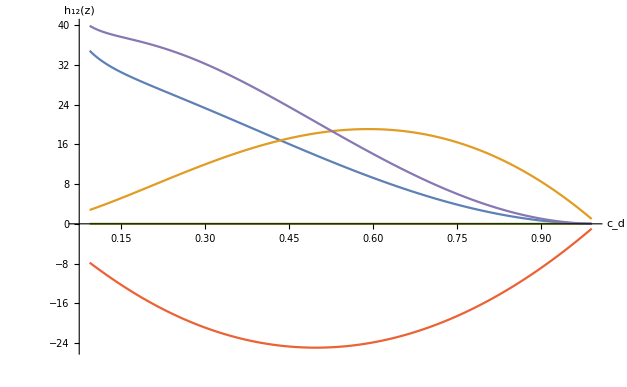

```mathematica
posγ=Flatten[Position[Flatten[hReadColumn[5,10,{"gamma"}]],5.]];
posϵ=Flatten[SelectPositions[Flatten[hReadColumn[5,10,{"epsilon"}]],#>0&]];
(* We limit the analyses to when the resource abundance is positive *)
pos=Intersection[posγ,posϵ];
h12split={hReadColumn[5,10,{"cd","h12"}][[pos]],hReadColumn[5,10,{"cd","hg12"}][[pos]],hReadColumn[5,10,{"cd","hee12"}][[pos]],hReadColumn[5,10,{"cd","hge12"}][[pos]],hReadColumn[5,10,{"cd","hre12"}][[pos]]};
ListLinePlot[h12split,PlotRange->All,AxesLabel->{ "c_d","h_12(z)"}]
(* In blue: Subscript[h, 12](z); in orange: Subscript[h, g,12](z); in green: Subscript[h, exe,12](z); in red: Subscript[h, gxe,12](z); in purple: Subscript[h, rxe,12](z)*)
```

We can first check visually the contribution of each term to  h_12(z) in the above graph. We can see  that  here, correlational selection between the attack rate and dispersal is always positive (blue curve). Additionally, we see by comparing the purple and blue curves that h_(12,rxe)(z)>h_12(z), so biased ecological inheritance is the main driver of this correlational selection in the above graph, especially where the cost of dispersal is not too strong.  In the following, we generalise those observations using the set of all parameters we tested.

```mathematica
readAll[element_]:=Flatten[{hReadColumn[5,10,element],hReadColumn[1,10,element],hReadColumn[0.5,10,element],hReadColumn[1,20,element],hReadColumn[0.5,20,element],hReadColumn[1,50,element],hReadColumn[0.5,50,element]},2];
```

```mathematica
NoExtinction=Flatten[SelectPositions[readAll[{"epsilon"}],#>0&]];
tot=Dimensions[NoExtinction][[1]];
valuesh12=readAll[{"h12"}];
valueshg12=readAll[{"hg12"}];
valueshee12=readAll[{"hee12"}];
valueshge12=readAll[{"hge12"}];
valueshre12=readAll[{"hre12"}];
valuesH=readAll[{"H"}];
```

We determine the contribution of the different terms of h_12(z) by checking the proportion of sets of parameters at which each element is positive.

(1)h_12>0 : correlational selection always favors a positive association between the attack rate and dispersal.

```mathematica
N[Dimensions[Select[valuesh12[[NoExtinction]],#>0&]][[1]]/tot]
(* showing Subscript[h, 12]>0  *)
```

1.

(2) h_(g,12)>0: Intra-generational interactions always favor a positive association between the attack rate and dispersal. However,their positive effects are almost always cancelled out by h_(12,gxe) (i.e. h_(g,12) + h_(gxe,12) tends to be negative or very small)

```mathematica
N[Dimensions[Select[valueshg12[[NoExtinction]],#>0&]][[1]]/tot]
(* showing Subscript[h, g,12]>0  *)
```

1.

```mathematica
N[Dimensions[Select[valueshge12[[NoExtinction]],# < 0&]][[1]]/tot]
(* showing Subscript[h, gxe,12] < 0  *)
```

1.

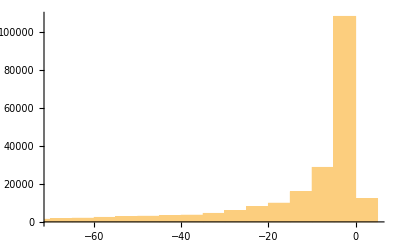

```mathematica
Histogram[(valueshge12+valueshg12)[[NoExtinction]]]
(* showing Subscript[h, g,12] + Subscript[h, gxe,12] is most often negative or weakly positive *)
```

```mathematica
(* with maximum value : *)
Max[(valueshge12+valueshg12)[[NoExtinction]]]
```

0.154085

Hence,the positive effect of intra-generational interactions on correlational selection are typically reversed or almost entirely cancelled out by the negative effect of h_(12,gxe)

(3) h_(exe,12):Environmentally-mediated interactions have no effect on correlational selection

```mathematica
N[Dimensions[Select[valueshee12[[NoExtinction]],#==0&]][[1]]/tot]
(* showing Subscript[h, 12,exe] = 0 as expected since dispersal has no direct effect on resource abundance  *)
```

1.

(4) h_(rxe,12)>0: Biased ecological inheritance always favors a positive association between dispersal and the attack rate

```mathematica
N[Dimensions[Select[valueshre12[[NoExtinction]],#>0&]][[1]]/tot]
(* showing Subscript[h, rxe,12]>0  *)
```

1.

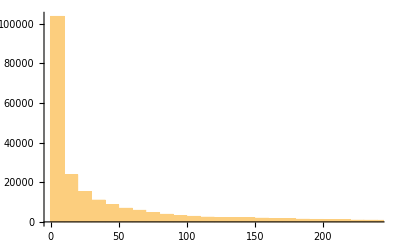

```mathematica
Histogram[Select[valueshre12[[NoExtinction]],#>0&]]
(* showing Subscript[h, rxe,12] can be large  *)
```

In conclusion, biased ecological inheritance is the main driver behind correlational selection being positive.

#### ii) Analyses of biased ecological inheritance

Here we show that h_(rxe,12) is positive because of the negative effect of the attack rate on the resource, and the negative effect of dispersal on relatedness (i.e.  show eq. (F - 14) in the appendix).

(1) Effect of the attack rate over one generation, weighted by the effect of resource abundance on fitness

```mathematica
Evaluate[D[w,ϵ]D[F,zi1]/.monopop/.ϵ->(ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1)];
%==-(1-λ^2)τ1 ⅇ^(-γ+n τ1 z1)/.λ->1-m//FullSimplify
```

True

This shows the first part of eq. (F - 14) is negative.

(2) Effect of dispersal on relatedness

Intuitively, it is clear that dispersal reduces inter - generational relatedness. However, the mathematical proof is not so straightforward. From eq. (D-48), we compute (∂(r̄)_(2,h)(ζ,z))/(∂ζ_p):

```mathematica
r2h=(1-m)^h dr2[z2all]((n-1)/n+1/(2r2 n))+D[wp,zi2]∑_(k=1)^(h-1) (1-m)^(h-k-1)r2k+(n-1)D[wp,zj2]∑_(k=1)^(h-1) (1-m)^(h-k-1)r3k+n D[wp,ϵ]D[F,zi2]∑_(k=1)^(h-1) (1-m)^(h-k-1)((D[F,ϵ])^(k-1)+∑_(l=1)^(k-1) (D[F,ϵ])^(l-1)+∑_(l=k+1)^∞ (D[F,ϵ])^(l-1))/.monopop/.ϵ->(ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1);
```

As dispersal has no impact on resource abundance, (∂F)/(∂z_2)=0. So (∂(r̄)_(2,h)(ζ,z))/(∂ζ_p)can  be simplified into

```mathematica
r2h==(1-m)^h dr2[z2all]((n-1)/n+1/(2r2 n))+D[wp,zi2]∑_(k=1)^(h-1) (1-m)^(h-k-1)r2k+(n-1)D[wp,zj2]∑_(k=1)^(h-1) (1-m)^(h-k-1)r3k/.monopop/.ϵ->(ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1)//FullSimplify
```

True

First, we show that dr2[z2all] < 0, i.e. that the effect of dispersal on intra - generational relatedness is always negative.

```mathematica
dr2[z2all]==(2 r2 n)/(1-z2)( λ rb3-rb2)/.monopop/.ϵ->(ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1)/.λ->1-m//FullSimplify
```

True

```mathematica
Reduce[Evaluate[(2 r2 n)/(1-z2)( λ rb3-rb2)/.λ->1-m]<0&&0<cd<1&&0<z2<1&&n>1]//FullSimplify
```

0<z2<1&&0<cd<1&&n>1

Let us now consider the remaining two terms of r2h above, which we find can be rewritten as :

```mathematica
D[wp,zi2]∑_(k=1)^(h-1) (1-m)^(h-k-1)r2k+(n-1)D[wp,zj2]∑_(k=1)^(h-1) (1-m)^(h-k-1)r3k==∑_(k=1)^(h-1) (1-m)^(h-k)(-(1/(1-z2))r2k+(1/(1-cd z2))((n-1)r3k+r2k)/n)/.monopop/.ϵ->(ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1)/.λ->1-m//FullSimplify
```

True

where
r2k=(r̄)_(2,k)^°=E^°[(Mt-k)/n] (eq. A-28) is the probability that two individuals k generations apart are IBD; and
r3k=(r̄)_(3,k)^°=E^°[(Mt-1)/(n-1)(Mt-k)/n] (eq. C-10) is the probability that three individuals, two sampled without replacement at the same generation and one sampled k generations before are all IBD.

From these definitions, we have that (((n-1)r3k+r2k)/n)= E^°[Mt/n(Mt-k)/n],which is thus the probability that three individuals,two sampled with replacement at the same generation and one sampled k generations before them,are all IBD. 
Hence, we must have r2k > ((n-1)r3k+r2k)/n  and so, ∑_(k=1)^(h-1) (1-m)^(h-k)(-(1/(1-z2))r2k+(1/(1-cd z2))((n-1)r3k+r2k)/n) < ∑_(k=1)^(h-1) (1-m)^(h-k)(-1/(1-z2)+1/(1-cd z2)) r2k  . But this term between brackets is always negative :

```mathematica
Reduce[-(1/(1-z2))+(1/(1-cd z2))<0&&0<cd<1&&0<z2<1]
```

0<z2<1&&0<cd<1

Hence (-(1/(1-z2))r2k+(1/(1-cd z2))((n-1)r3k+r2k)/n)  is always negative. Putting everything together,we see the effect of dispersal on inter-generational relatedness is always negative (second part of eq.(F-16)).

(3) Effect of ecological inheritance

Finally, the last part of eq. F14:

```mathematica
Evaluate[D[F,ϵ]/.monopop/.ϵ->(ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1)];
%== ⅇ^(-γ+n τ1 z1)/.λ->1-m//FullSimplify
```

True

which is always positive also when γ > τ_1N z_1.

### D. Figure 2B - Conditions for stabilizing and disruptive selection when the attack rate co-evolves with dispersal

This is the code for producing Fig. 2B of the main text :

```mathematica
FigH[τ1para_,npara_]:=ListContourPlot[hReadColumn[τ1para,npara,{"cd","gamma","H"}],PlotRange->All,Contours->{0.},ColorFunction->(Blend[{Transparent,LightGray},#1]&),FrameLabel->{"Cost of dispersal, c_d","Renewal rate, γ"},LabelStyle->{FontFamily->"Arial",FontSize->18,FontColor->Black},PlotRangePadding->0,GridLines->None,Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},ImageSize->Medium,FrameTicks->{{1,2,3,4,5,6},{{0.2,0.4,0.6,0.8},{0.2,0.4,0.6,0.8}}},FrameStyle->Black,FrameTicksStyle->{{Black,Directive[FontOpacity->0,FontSize->0]},{Black,Directive[FontOpacity->0,FontSize->0]}},InterpolationOrder->1,PlotLegends->None];
```

```mathematica
FigHτ5=FigH[5,10];
FigHτ1=FigH[1,10];
FigHτ05=FigH[0.5,10];
```

```mathematica
Fig2=GraphicsGrid[{{Show[FigHτ5,Figτ5,PlotLabel->Style["i. τ_1 = 5",FontColor->Black,FontSize->20,FontFamily->"Arial"]],Show[FigHτ1,Figτ1,FrameLabel->{"Cost of dispersal, c_d"," "},PlotLabel->Style["ii. τ_1 = 1",FontColor->Black,FontSize->20,FontFamily->"Arial"]],Show[FigHτ05,Figτ05,FrameLabel->{"Cost of dispersal, c_d"," "},PlotLabel->Style["iii. τ_1 = 0.5",FontColor->Black,FontSize->20,FontFamily->"Arial"]]}},ImageSize->{900,300},Spacings->Scaled[-0.15],LabelStyle->{FontFamily->"Arial",FontSize->19,FontColor->Black}]
```

-Graphics-

## 5. Supplementary Figure S4: Effect of patch size N

Here are the codes for producing Supplementary Figure S4 A and B.

### A- Supplementary Figure S4-A

```mathematica
FigS2Ai=Plot[Evaluate[SuperStar[z2]/.cd->{0.1}],{n,1.,50},PlotRange->{0,1},PlotStyle->{{Black, Thick},{Gray, Thick}},FrameStyle->{{Black,White},{Black,White}},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{1,10,20,30,40,50},None}},LabelStyle->{FontFamily->"Arial",FontSize->18},PlotRangePadding->{{-0.9,0.11},0.001},Frame->True,FrameLabel->{"Patch size, N",Rotate["z_2^*",-π/2]},AspectRatio->0.8,Background->None,ImageSize->Medium,PlotLabel->Style["Singular dispersal",FontColor->Black,FontSize->20],Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];
```

```mathematica
values={cd->0.1,τ1->1};
```

```mathematica
SuperStar[valuesNz1]=Table[
ϕ=Min[1,Evaluate[(γ-Log[λ])/(n τ1)/.λ->1-m/.z2->SuperStar[z2]/.values/.n->nN/.γ->γN]];
δ=0.000000001;
SuperStar[z1]=z1/.Flatten[FindRoot[Evaluate[ s1 == 0 /.λ->1-m/.z2->SuperStar[z2]/.values/.n->nN/.γ->γN],{z1,δ,ϕ-δ}]];
{nN,SuperStar[z1]},{γN,3,5,2.},{nN,1,50,1}];
```

```mathematica
FigS2Aii=ListLinePlot[SuperStar[valuesNz1],PlotStyle->{{Gray,Thick},{Black,Thick}} ,Frame->True,PlotRange->{0,0.47},FrameStyle->{{Black,White},{Black,White}},FrameTicks->{{{0,0.1,0.2,0.3,0.4},None},{{1,10,20,30,40,50},None}},PlotRangePadding->{{-1,0.11},0.00},
LabelStyle->{FontFamily->"Arial",FontSize->18},PlotRangePadding->{0,0.},FrameLabel->{"Patch size, N",Rotate["z_1^*",-π/2]},AspectRatio->0.8,ImageSize->Medium,PlotLabel->Style["Singular attack rate",FontColor->Black,FontSize->20],RotateLabel->False,Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];
```

```mathematica
valuesE=Table[
ϕ=Min[1,Evaluate[(γ-Log[λ])/(n τ1)/.λ->1-m/.z2->SuperStar[z2]/.values/.n->nN/.γ->γN]];
δ=0.000000001;
SuperStar[z1]=z1/.Flatten[FindRoot[Evaluate[ s1 == 0 /.λ->1-m/.z2->SuperStar[z2]/.values/.n->nN/.γ->γN],{z1,δ,ϕ-δ}]];
ϵ̂=Max[ (ⅇ^γ-ⅇ^(n τ1 z1))/(ⅇ^γ-1),0]/.z1->SuperStar[z1]/.values/.n->nN/.γ->γN;

{nN,ϵ̂},{γN,3,5,2.},{nN,1,50,1}];
```

```mathematica
FigS2Aiii=ListLinePlot[valuesE,PlotStyle->{{Gray,Thick},{Black,Thick}} ,Frame->True,PlotRange->{0,01},FrameStyle->{{Black,White},{Black,White}},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{1,10,20,30,40,50},None}},PlotRangePadding->{{-1,0.15},0.00},
LabelStyle->{FontFamily->"Arial",FontSize->18},PlotRangePadding->{0,0.},FrameLabel->{"Patch size, N",Rotate["ϵ̂",-π/2]},AspectRatio->0.8,ImageSize->Medium,PlotLabel->Style["Ecological equilibrium",FontColor->Black,FontSize->20],RotateLabel->False,Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];
```

```mathematica
FigS2A=GraphicsGrid[{{Graphics[FigS2Ai],Graphics[FigS2Aii],Graphics[FigS2Aiii]}},Spacings->Scaled[-0.2],ImageSize->{900,300}]
```

-Graphics-

### B- Supplementary Figure S4-B

```mathematica
Figτ05n20=Show[FigH[0.5,20],Figh11[0.5,20],FigExinction[0.5,20]];
Figτ1n20=Show[FigH[1,20],Figh11[1,20],FigExinction[1,20]];
```

```mathematica
FigS2=GraphicsGrid[{{Show[Figτ1n20,LabelStyle->{FontFamily->"Arial",FontSize->19,FontColor->Black},FrameLabel->{"Cost of dispersal, c_d","Renewal rate, γ"}],Show[Figτ05n20,LabelStyle->{FontFamily->"Arial",FontSize->19,FontColor->Black},FrameLabel->{"Cost of dispersal, c_d",None}]}},ImageSize->{600,300},Spacings->Scaled[-0.12]]
```

-Graphics-